# Appendix

Key:

E[t]: Elephants

P[t]: Predators

F[t]: Effort

h[t]: Hunting

g_E: Growth$Elephants

g_P: Growth$Predators

E_max: Elephants$Max

P_max: Predators$Max

ϵ_E: Eaten

ϵ_P: Eating

ϕ: Hunting$Efficiency

p: Price$Ivory

c_1: c1

η: Elasticity1

ADD

### Elephant-Predator Growth Models

```mathematica
(*Predator-Prey model*)
Dt$Elephants[Growth$Elephants_,Elephants_,Elephants$Max_,Hunting_,Eaten_,Predators_]:=Growth$Elephants*(1-Elephants/Elephants$Max)*Elephants-Hunting*Elephants-Eaten*Elephants*Predators

Dt$Predators[Growth$Predators_,Predators_,Predators$Max_,Eating_,Elephants_]:=Growth$Predators*(1-Predators/Predators$Max)*Predators+Eating*Elephants*Predators
```

### Figure 1.1

{{Elephants→0,Predators→Predators$Max},{Elephants→-(-Elephants$Max Growth$Elephants Growth$Predators+Elephants$Max Growth$Predators Hunting+Eaten Elephants$Max Growth$Predators Predators$Max)/(Growth$Elephants Growth$Predators+Eaten Eating Elephants$Max Predators$Max),Predators→((Eating Elephants$Max Growth$Elephants+Growth$Elephants Growth$Predators-Eating Elephants$Max Hunting) Predators$Max)/(Growth$Elephants Growth$Predators+Eaten Eating Elephants$Max Predators$Max)},{Elephants→0,Predators→0},{Elephants→(Elephants$Max (Growth$Elephants-Hunting))/Growth$Elephants,Predators→0}}

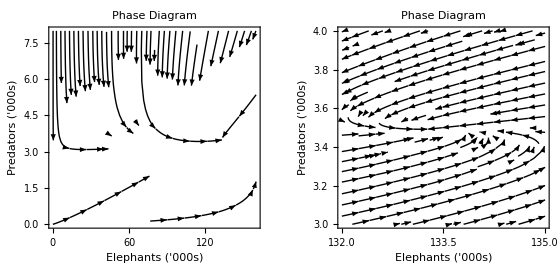

{133.269,3.49176}

```mathematica
(*Vector of Parameters*)
Parameters$Elephants$Predators={Growth$Elephants,Elephants$Max,Hunting,Eaten,Growth$Predators,Predators$Max,Eating};

(*Special Parameters*)
Parameters$Elephants$Predators$NoHunting=Parameters$Elephants$Predators/.{Growth$Elephants->0.09,Elephants$Max->200,Hunting->0,Eaten->0.0086,Growth$Predators->0.1,Predators$Max->3,Eating->0.000123};

(*Phase Plot*)
Phaseplot$PredatorPrey$1[Growth$Elephants_,Elephants$Max_,Hunting_,Eaten_,Growth$Predators_,Predators$Max_,Eating_,Elephants$AxisMin_,Elephants$AxisMax_,Predators$AxisMin_,Predators$AxisMax_]:=StreamPlot[{Dt$Elephants[Growth$Elephants,Elephants,Elephants$Max,Hunting,Eaten,Predators],Dt$Predators[Growth$Predators,Predators,Predators$Max,Eating,Elephants]},{Elephants,Elephants$AxisMin,Elephants$AxisMax},{Predators,Predators$AxisMin,Predators$AxisMax},PlotLabel->"Phase Diagram",FrameLabel->{"Elephants ('000s)","Predators ('000s)"},PlotTheme->"Monochrome",StreamPoints->{400,Scaled[0.01]},PlotRange->{{Elephants$AxisMin,Elephants$AxisMax},{Predators$AxisMin,Predators$AxisMax}}]

(*Steady State Solution*)
Solve[{0==Dt$Elephants[Growth$Elephants,Elephants,Elephants$Max,Hunting,Eaten,Predators],0==Dt$Predators[Growth$Predators,Predators,Predators$Max,Eating,Elephants]},{Elephants,Predators}]


(*Steady State*)
LinearEstimate$Elephants$Predators[Growth$Elephants_,Elephants$Max_,Hunting_,Eaten_,Growth$Predators_,Predators$Max_,Eating_]:={-((-Elephants$Max Growth$Elephants Growth$Predators+Elephants$Max Growth$Predators Hunting+Eaten Elephants$Max Growth$Predators Predators$Max)/(Growth$Elephants Growth$Predators+Eaten Eating Elephants$Max Predators$Max)),((Eating Elephants$Max Growth$Elephants+Growth$Elephants Growth$Predators-Eating Elephants$Max Hunting) Predators$Max)/(Growth$Elephants Growth$Predators+Eaten Eating Elephants$Max Predators$Max)};

(*Special Phase Plot No Hunting*)
GraphicsGrid[{{Phaseplot$PredatorPrey$1@@Join[Parameters$Elephants$Predators$NoHunting,{0,160,0,8}(*PlotRange*)],Phaseplot$PredatorPrey$1@@Join[Parameters$Elephants$Predators$NoHunting,{132,135,3,4}(*PlotRange*)]}},Frame->True]
(*Special Steady State No Hunting*)
LinearEstimate$Elephants$Predators@@Parameters$Elephants$Predators$NoHunting
```

### Eigenvalues for Figure 1.1

```mathematica
(*Jacobian Function*)
Jacobian$Elephants$Predators[Elephants_,Predators_,Growth$Elephants_,Elephants$Max_,Hunting_,Eaten_,Growth$Predators_,Predators$Max_,Eating_]:={{(1-Elephants/Elephants$Max) Growth$Elephants-(Elephants Growth$Elephants)/Elephants$Max-Hunting-Eaten Predators,-Eaten Elephants},{Eating Predators,Eating Elephants+Growth$Predators (1-Predators/Predators$Max)-(Growth$Predators Predators)/Predators$Max}}
(*Special Eigenvalues and Eigenvectors of Jacobian for No Hunting*)
Eigensystem[Jacobian$Elephants$Predators@@Join[LinearEstimate$Elephants$Predators@@Parameters$Elephants$Predators$NoHunting(*Elephants,Predators*),Parameters$Elephants$Predators$NoHunting]]
```

{{-0.105606,-0.0707574},{{0.999208,0.0397855},{0.999956,0.00941099}}}

### Figure 1.2

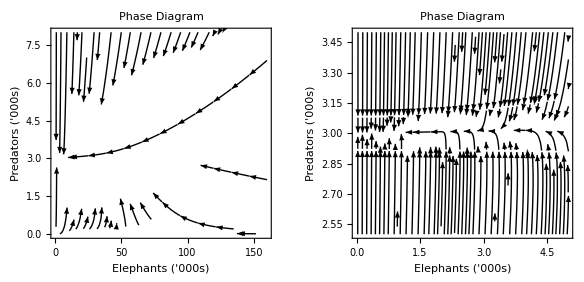

{2.30464×10^-14,3.}

```mathematica
Parameters$Elephants$Predators$Hunting=Parameters$Elephants$Predators/.{Growth$Elephants->0.09,Elephants$Max->200,Hunting->0.0642,Eaten->0.0086,Growth$Predators->0.1,Predators$Max->3,Eating->0.000123};

(*Special Phase Plot With Hunting*)
GraphicsGrid[{{Phaseplot$PredatorPrey$1@@Join[Parameters$Elephants$Predators$Hunting,{0,160,0,8}(*PlotRange*)],Phaseplot$PredatorPrey$1@@Join[Parameters$Elephants$Predators$Hunting,{0,5,2.5,3.5}(*PlotRange*)]}},Frame->True]

(*Special Steady State With Hunting*)
LinearEstimate$Elephants$Predators@@Parameters$Elephants$Predators$Hunting
```

### Figure 2.1.3

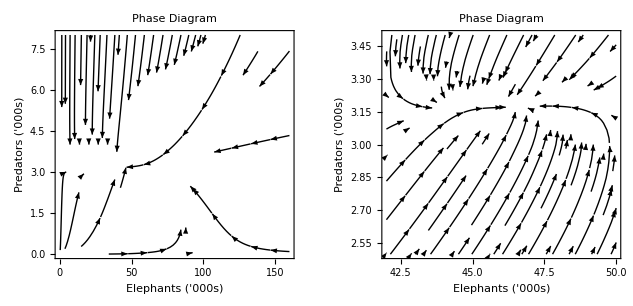

{46.1538,3.17031}

```mathematica
Parameters$Elephants$Predators$Hunting=Parameters$Elephants$Predators/.{Growth$Elephants->0.09,Elephants$Max->200,Hunting->0.645633*0.065,Eaten->0.0086,Growth$Predators->0.1,Predators$Max->3,Eating->0.000123};

(*Special Phase Plot With Hunting*)
GraphicsGrid[{{Phaseplot$PredatorPrey$1@@Join[Parameters$Elephants$Predators$Hunting,{0,160,0,8}(*PlotRange*)],Phaseplot$PredatorPrey$1@@Join[Parameters$Elephants$Predators$Hunting,{42,50,2.5,3.5}(*PlotRange*)]}},Frame->True]

(*Special Steady State With Hunting*)
LinearEstimate$Elephants$Predators@@Parameters$Elephants$Predators$Hunting
```

### Figure 2.1.4

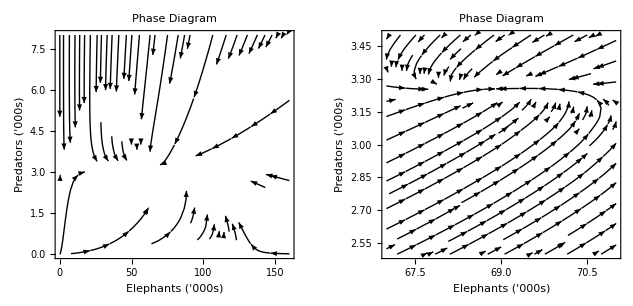

{68.9038,3.25425}

```mathematica
Parameters$Elephants$Predators$Hunting=Parameters$Elephants$Predators/.{Growth$Elephants->0.09,Elephants$Max->200,Hunting->0.031006703630005985,Eaten->0.0086,Growth$Predators->0.1,Predators$Max->3,Eating->0.000123};

(*Special Phase Plot With Hunting*)
GraphicsGrid[{{Phaseplot$PredatorPrey$1@@Join[Parameters$Elephants$Predators$Hunting,{0,160,0,8}(*PlotRange*)],Phaseplot$PredatorPrey$1@@Join[Parameters$Elephants$Predators$Hunting,{67,71,2.5,3.5}(*PlotRange*)]}},Frame->True]

(*Special Steady State With Hunting*)
LinearEstimate$Elephants$Predators@@Parameters$Elephants$Predators$Hunting
```

### Figure 2.1.5

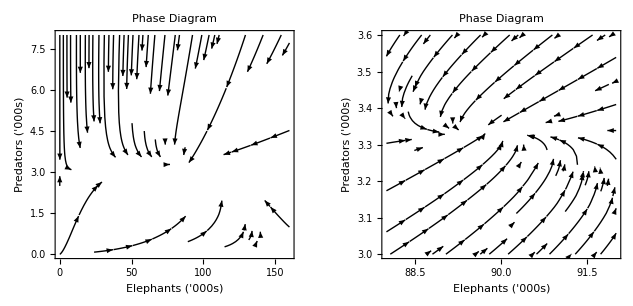

{89.7112,3.33103}

```mathematica
Parameters$Elephants$Predators$Hunting=Parameters$Elephants$Predators/.{Growth$Elephants->0.09,Elephants$Max->200,Hunting->0.32281633136094684*0.065,Eaten->0.0086,Growth$Predators->0.1,Predators$Max->3,Eating->0.000123};

(*Special Phase Plot With Hunting*)
GraphicsGrid[{{Phaseplot$PredatorPrey$1@@Join[Parameters$Elephants$Predators$Hunting,{0,160,0,8}(*PlotRange*)],Phaseplot$PredatorPrey$1@@Join[Parameters$Elephants$Predators$Hunting,{88,92,3,3.6}(*PlotRange*)]}},Frame->True]

(*Special Steady State With Hunting*)
LinearEstimate$Elephants$Predators@@Parameters$Elephants$Predators$Hunting
```

### Figure 2.1.6

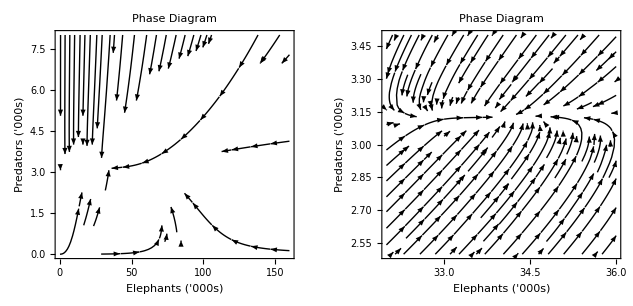

{33.8462,3.12489}

```mathematica
Parameters$Elephants$Predators$Hunting=Parameters$Elephants$Predators/.{Growth$Elephants->0.09,Elephants$Max->200,Hunting->0.7368485680473373*0.065,Eaten->0.0086,Growth$Predators->0.1,Predators$Max->3,Eating->0.000123};

(*Special Phase Plot With Hunting*)
GraphicsGrid[{{Phaseplot$PredatorPrey$1@@Join[Parameters$Elephants$Predators$Hunting,{0,160,0,8}(*PlotRange*)],Phaseplot$PredatorPrey$1@@Join[Parameters$Elephants$Predators$Hunting,{32,36,2.5,3.5}(*PlotRange*)]}},Frame->True]

(*Special Steady State With Hunting*)
LinearEstimate$Elephants$Predators@@Parameters$Elephants$Predators$Hunting
```

### Figure 2.1.1

Elephants→68.9038

Predators→3.25425

2.13648

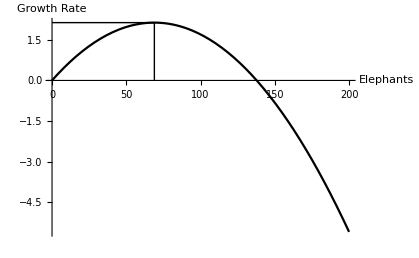

```mathematica
(*Derivative of Elephant growth rate expression with NO HUNTING*)
D[(Dt$Elephants[Growth$Elephants,Elephants,Elephants$Max,Hunting,Eaten,Predators]+Hunting*Elephants(*Removes hunting from expression*)),Elephants];

(*Steady-state number of predators*)
Steady$State$Predators=Solve[Growth$Predators*(1-Predators/Predators$Max)*Predators+Eating*Elephants*Predators==0,Predators][[2]][[1]];
(*FOC for maximising Elephant growth rate given predators are in  Steady State*)
Elephants$For$Growth$Max=Solve[(((1-Elephants/Elephants$Max) Growth$Elephants-(Elephants Growth$Elephants)/Elephants$Max-Eaten Predators)/.{Steady$State$Predators})==0,Elephants];

(*Substituting into growth equation for elephants to obtain maximum sustainable yield expression*)
(Dt$Elephants[Growth$Elephants,Elephants,Elephants$Max,Hunting,Eaten,Predators]+Hunting*Elephants)/.Elephants$For$Growth$Max;

(*Maximum sustainable yield number of elephants*)
Special$Elephants$For$MSY=Flatten[Elephants$For$Growth$Max/.{Growth$Elephants->0.09,Elephants$Max->200,Hunting->0,Eaten->0.0086,Growth$Predators->0.1,Predators$Max->3,Eating->0.000123}][[1]]

(*Steady-state number of predators with special parameters*)
Special$Predators$For$MSY=(Steady$State$Predators)/.Special$Elephants$For$MSY/.{Growth$Elephants->0.09,Elephants$Max->200,Hunting->0,Eaten->0.0086,Growth$Predators->0.1,Predators$Max->3,Eating->0.000123}

(*Maximum sustainable yield*)
Special$MSY=Dt$Elephants[Growth$Elephants,Elephants,Elephants$Max,Hunting,Eaten,Predators]/.{Special$Elephants$For$MSY,Special$Predators$For$MSY,Growth$Elephants->0.09,Elephants$Max->200,Hunting->0,Eaten->0.0086,Growth$Predators->0.1,Predators$Max->3,Eating->0.000123}

(*Maximum sustainable yield Hunting level*)
Special$Hunting$For$MSY=(Special$MSY/(Elephants/.Special$Elephants$For$MSY));

(*Plotting Growth Rate*)
Plot[{Dt$Elephants[0.09,Elephants,200,0,0.0086,Predators]/.Special$Predators$For$MSY},{Elephants,0,200},Epilog->{Line[{{Elephants/.Special$Elephants$For$MSY,0},{Elephants/.Special$Elephants$For$MSY,Special$MSY}}],Line[{{0,Special$MSY},{Elephants/.Special$Elephants$For$MSY,Special$MSY}}]},AxesLabel->{"Elephants","Growth Rate"},PlotTheme->"Monochrome"]
```

### Figure 2.1.2

Effort→0.322816

Effort→0.493846

Effort→0.645633

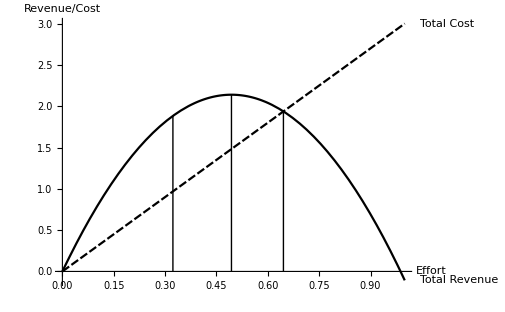

```mathematica
(*Instantaneous Profit Expression*)
Profit[Price$Ivory_,Hunting$Efficiency_,Effort_,Elephants_,c1_]:=(Price$Ivory*Hunting$Efficiency*Effort*Elephants-c1*Effort)

(*Elephant Population Growth Expression*)
Dt$Elephants[Growth$Elephants_,Elephants_,Elephants$Max_,Hunting$Efficiency_,Effort_,Eaten_,Predators_]:=Growth$Elephants*(1-Elephants/Elephants$Max)*Elephants-Hunting$Efficiency*Effort*Elephants-Eaten*Elephants*Predators
(*Steady-state number of predators*)
Steady$State$Predators=Solve[Growth$Predators*(1-Predators/Predators$Max)*Predators+Eating*Elephants*Predators==0,Predators][[2]][[1]];

(*Steady State level of Elephants as a function of Effort with predators in the function*)
Steady$State$Elephants$WithPredators=Solve[Dt$Elephants[Growth$Elephants,Elephants,Elephants$Max,Hunting$Efficiency,Effort,Eaten,Predators]==0,Elephants][[2]][[1]];

(*Steady State level of Elephants as a function of Effort without predators in the function, found by substituting steady state level of predators*)
Steady$State$Elephants=Solve[{Equal@@Steady$State$Elephants$WithPredators/.Steady$State$Predators},Elephants][[1]][[1]];

(*Substitute Steady$State$Elephants into Revenue to obtain expression for sustainable total revenue*)
Total$Revenue$Sustainable=(Price$Ivory*Hunting$Efficiency*Effort*Elephants)/.{Steady$State$Elephants};

(*Substitute into profit function*)
(*FOC with respect to Effort, Profit maximising effort*)
Solve[D[Profit[Price$Ivory,Hunting$Efficiency,Effort,Elephants,c1]/.{Steady$State$Elephants},Effort]==0,Effort][[1]][[1]];

(*Special Vector of Parameters*)
Special$Parameters$Static={Growth$Elephants->0.09,Elephants$Max->200,Hunting->0,Eaten->0.0086,Growth$Predators->0.1,Predators$Max->3,Eating->0.000123,Hunting$Efficiency->0.065,Price$Ivory->1,c1->3};

(*Special profit maximising effort*)
Special$Effort$For$MEY=Solve[D[Profit[Price$Ivory,Hunting$Efficiency,Effort,Elephants,c1]/.{Steady$State$Elephants},Effort]==0,Effort][[1]][[1]]/.Special$Parameters$Static

(*Special Maximum sustainable yield level of effort*)
Special$Effort$For$MSY=(Solve[D[Total$Revenue$Sustainable,Effort]==0,Effort]/.Special$Parameters$Static)[[1]][[1]]

(*Special Bionomic Equilibrium*)
Special$Effort$For$BE=Solve[Total$Revenue$Sustainable==c1*Effort,Effort][[2]][[1]]/.Special$Parameters$Static

(*Special Plot*)
Plot[{Total$Revenue$Sustainable/.Special$Parameters$Static,(c1*Effort)/.Special$Parameters$Static},{Effort,0,1},Epilog->{Line[{{Effort/.Special$Effort$For$MEY,0},{Effort/.Special$Effort$For$MEY,Total$Revenue$Sustainable/.Special$Parameters$Static/.Special$Effort$For$MEY}}],Line[{{Effort/.Special$Effort$For$MSY,0},{Effort/.Special$Effort$For$MSY,Total$Revenue$Sustainable/.Special$Parameters$Static/.Special$Effort$For$MSY}}],Line[{{Effort/.Special$Effort$For$BE,0},{Effort/.Special$Effort$For$BE,Total$Revenue$Sustainable/.Special$Parameters$Static/.Special$Effort$For$BE}}]},AxesLabel->{"Effort","Revenue/Cost"},
PlotLabels->{"Total Revenue","Total Cost"},PlotTheme->"Monochrome"]

Clear[Special$Parameters$Static]
```

### Adjusted Gordon-Schaefer model for Figure 2.1.6

Effort→0.368424

Effort→0.493846

Effort→0.736849

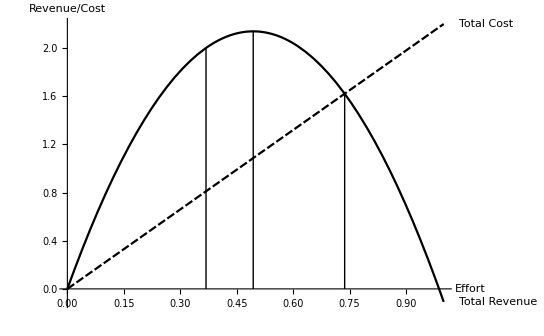

```mathematica
(*Special Vector of Parameters*)
Special$Parameters$Static={Growth$Elephants->0.09,Elephants$Max->200,Hunting->0,Eaten->0.0086,Growth$Predators->0.1,Predators$Max->3,Eating->0.000123,Hunting$Efficiency->0.065,Price$Ivory->1,c1->2.2};

(*Special profit maximising effort*)
Special$Effort$For$MEY=Solve[D[Profit[Price$Ivory,Hunting$Efficiency,Effort,Elephants,c1]/.{Steady$State$Elephants},Effort]==0,Effort][[1]][[1]]/.Special$Parameters$Static

(*Special Maximum sustainable yield level of effort*)
Special$Effort$For$MSY=(Solve[D[Total$Revenue$Sustainable,Effort]==0,Effort]/.Special$Parameters$Static)[[1]][[1]]

(*Special Bionomic Equilibrium*)
Special$Effort$For$BE=Solve[Total$Revenue$Sustainable==c1*Effort,Effort][[2]][[1]]/.Special$Parameters$Static

(*Special Plot*)
Plot[{Total$Revenue$Sustainable/.Special$Parameters$Static,(c1*Effort)/.Special$Parameters$Static},{Effort,0,1},Epilog->{Line[{{Effort/.Special$Effort$For$MEY,0},{Effort/.Special$Effort$For$MEY,Total$Revenue$Sustainable/.Special$Parameters$Static/.Special$Effort$For$MEY}}],Line[{{Effort/.Special$Effort$For$MSY,0},{Effort/.Special$Effort$For$MSY,Total$Revenue$Sustainable/.Special$Parameters$Static/.Special$Effort$For$MSY}}],Line[{{Effort/.Special$Effort$For$BE,0},{Effort/.Special$Effort$For$BE,Total$Revenue$Sustainable/.Special$Parameters$Static/.Special$Effort$For$BE}}]},AxesLabel->{"Effort","Revenue/Cost"},
PlotLabels->{"Total Revenue","Total Cost"},PlotTheme->"Monochrome"]

Clear[Special$Parameters$Static]
```

### Figure 2.2.1

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

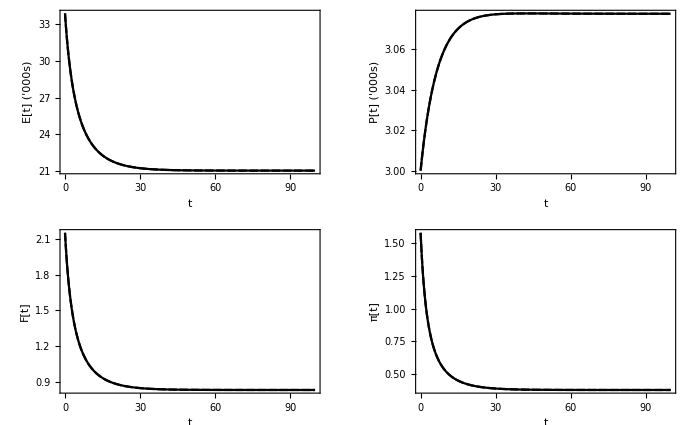

```mathematica
(*Maximising instantaneous profit*)
Equal@@Solve[D[-c1 (Effort[t])^Elasticity1+Hunting$Efficiency Price$Ivory Effort[t] Elephants[t],Effort[t]]==0,Effort[t]][[1]][[1]];

(*Dynamic path plot*)
Dynamic$Path1[Growth$Elephants_,Elephants$Max_,Hunting_,Eaten_,Growth$Predators_,Predators$Max_,Eating_,Hunting$Efficiency_,Price$Ivory_,c1_,Interest$Rate_,Elasticity1_,Elephants0_, Predators0_]:=NDSolve[{Effort[t]==((Hunting$Efficiency Price$Ivory Elephants[t])/(c1 Elasticity1))^(1/(-1+Elasticity1))(*Firm FOC*),Elephants[t] (Growth$Elephants-Hunting$Efficiency Effort[t]-Eaten Predators[t])==(Growth$Elephants Elephants[t]^2)/Elephants$Max+Elephants'[t](*Elephant Growth*), Growth$Predators*(1-Predators[t]/Predators$Max)*Predators[t]+Eating*Elephants[t]*Predators[t]==Predators'[t](*Predator Growth*),(*Profit*)Profit1[t]==-c1 (Effort[t])^Elasticity1+Hunting$Efficiency Price$Ivory Effort[t] Elephants[t],Elephants[0]==Elephants0,Predators[0]==Predators0, Effort[0]==1},{Elephants[t], Effort[t],Predators[t],Profit1[t]},{t,0,10000} ]


Dynamic$Path1$Plot[t$Max_]:=GraphicsGrid[{{Plot[{Elephants[t]/.Dynamic$Solution1,Elephants[t]/.Dynamic$Solution2},{t,0,t$Max},Frame->True,FrameLabel->{"t","E[t] ('000s)"},PlotRange->Full,PlotTheme->"Monochrome"],Plot[{Predators[t]/.Dynamic$Solution1,Predators[t]/.Dynamic$Solution2},{t,0,t$Max},Frame->True,FrameLabel->{"t","P[t] ('000s)"},PlotRange->Full,PlotTheme->"Monochrome"]},{Plot[{Effort[t]/.Dynamic$Solution1,Effort[t]/.Dynamic$Solution2},{t,0,t$Max},PlotRange->Full,Frame->True,FrameLabel->{"t","F[t]"},PlotTheme->"Monochrome"],
Plot[{Profit1[t]/.Dynamic$Solution1,Profit1[t]/.Dynamic$Solution2},{t,0,t$Max},PlotRange->Full,Frame->True,FrameLabel->{"t","π[t]"},PlotTheme->"Monochrome"]
}},Frame->True]

(*Substituting Special Parameters*)
Dynamic$Solution1=Dynamic$Path1@@({Growth$Elephants,Elephants$Max,Hunting,Eaten,Growth$Predators,Predators$Max,Eating,Hunting$Efficiency,Price$Ivory,c1,Interest$Rate,Elasticity1,Elephants0,Predators0}/.{Growth$Elephants->0.09,Elephants$Max->200,Hunting->0,Eaten->0.0086,Growth$Predators->0.1,Predators$Max->3,Eating->0.000123,Hunting$Efficiency->0.065,Price$Ivory->1,c1->1,Interest$Rate->0.035,Elasticity1->1.5,Elephants0->34,Predators0->3});

Dynamic$Solution2=Dynamic$Path1@@({Growth$Elephants,Elephants$Max,Hunting,Eaten,Growth$Predators,Predators$Max,Eating,Hunting$Efficiency,Price$Ivory,c1,Interest$Rate,Elasticity1,Elephants0,Predators0}/.{Growth$Elephants->0.09,Elephants$Max->200,Hunting->0,Eaten->0.0086,Growth$Predators->0.1,Predators$Max->3,Eating->0.000123,Hunting$Efficiency->0.065,Price$Ivory->1,c1->1,Interest$Rate->0.035,Elasticity1->1.5,Elephants0->34,Predators0->3});


Dynamic$Path1$Plot[100]

Elephants[t]/.Dynamic$Solution1/.t->100;
Effort[t]/.Dynamic$Solution1/.t->100;
Profit1[t]/.Dynamic$Solution1/.t->100;

Clear[Dynamic$Solution1,Dynamic$Solution2]
```

### Increasing cost from 1 to 1.5 in Figure 2.2.1 (Solid line is baseline plot)

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

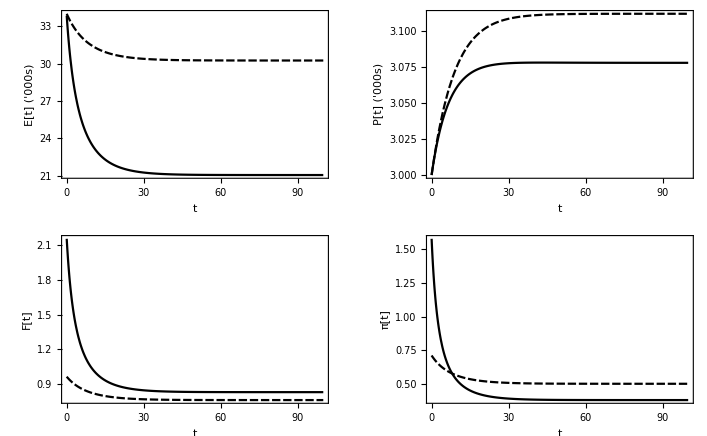

```mathematica
(*Substituting Special Parameters*)
Dynamic$Solution1=Dynamic$Path1@@({Growth$Elephants,Elephants$Max,Hunting,Eaten,Growth$Predators,Predators$Max,Eating,Hunting$Efficiency,Price$Ivory,c1,Interest$Rate,Elasticity1,Elephants0,Predators0}/.{Growth$Elephants->0.09,Elephants$Max->200,Hunting->0,Eaten->0.0086,Growth$Predators->0.1,Predators$Max->3,Eating->0.000123,Hunting$Efficiency->0.065,Price$Ivory->1,c1->1,Interest$Rate->0.035,Elasticity1->1.5,Elephants0->34,Predators0->3});

Dynamic$Solution2=Dynamic$Path1@@({Growth$Elephants,Elephants$Max,Hunting,Eaten,Growth$Predators,Predators$Max,Eating,Hunting$Efficiency,Price$Ivory,c1,Interest$Rate,Elasticity1,Elephants0,Predators0}/.{Growth$Elephants->0.09,Elephants$Max->200,Hunting->0,Eaten->0.0086,Growth$Predators->0.1,Predators$Max->3,Eating->0.000123,Hunting$Efficiency->0.065,Price$Ivory->1,c1->1.5,Interest$Rate->0.035,Elasticity1->1.5,Elephants0->34,Predators0->3});


Dynamic$Path1$Plot[100]

Clear[Dynamic$Solution1,Dynamic$Solution2]
```

### Increasing output elasticity from 1.5 to 2 in Figure 2.2.1 (Solid line is baseline plot)

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

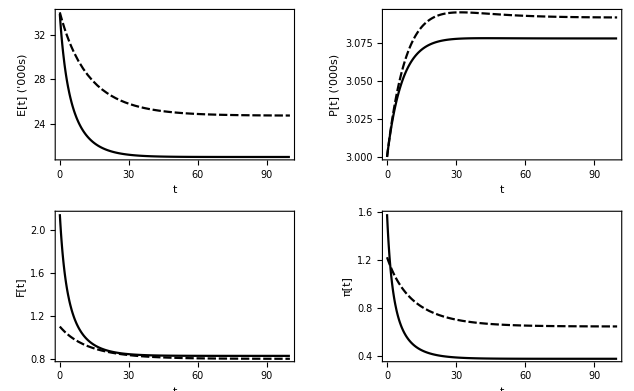

```mathematica
(*Substituting Special Parameters*)
Dynamic$Solution1=Dynamic$Path1@@({Growth$Elephants,Elephants$Max,Hunting,Eaten,Growth$Predators,Predators$Max,Eating,Hunting$Efficiency,Price$Ivory,c1,Interest$Rate,Elasticity1,Elephants0,Predators0}/.{Growth$Elephants->0.09,Elephants$Max->200,Hunting->0,Eaten->0.0086,Growth$Predators->0.1,Predators$Max->3,Eating->0.000123,Hunting$Efficiency->0.065,Price$Ivory->1,c1->1,Interest$Rate->0.035,Elasticity1->1.5,Elephants0->34,Predators0->3});

Dynamic$Solution2=Dynamic$Path1@@({Growth$Elephants,Elephants$Max,Hunting,Eaten,Growth$Predators,Predators$Max,Eating,Hunting$Efficiency,Price$Ivory,c1,Interest$Rate,Elasticity1,Elephants0,Predators0}/.{Growth$Elephants->0.09,Elephants$Max->200,Hunting->0,Eaten->0.0086,Growth$Predators->0.1,Predators$Max->3,Eating->0.000123,Hunting$Efficiency->0.065,Price$Ivory->1,c1->1,Interest$Rate->0.035,Elasticity1->2,Elephants0->34,Predators0->3});


Dynamic$Path1$Plot[100]

Clear[Dynamic$Solution1,Dynamic$Solution2]
```

### Increasing ivory price from 1 to 10 in Figure 2.2.1 (Solid line is baseline plot)

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

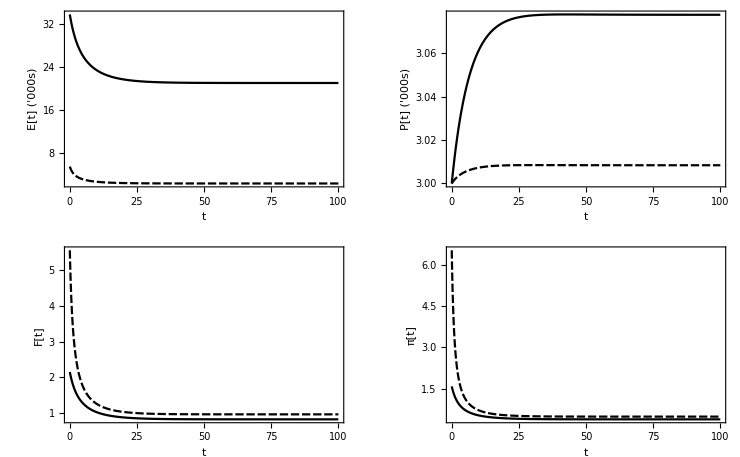

```mathematica
(*Substituting Special Parameters*)
Dynamic$Solution1=Dynamic$Path1@@({Growth$Elephants,Elephants$Max,Hunting,Eaten,Growth$Predators,Predators$Max,Eating,Hunting$Efficiency,Price$Ivory,c1,Interest$Rate,Elasticity1,Elephants0,Predators0}/.{Growth$Elephants->0.09,Elephants$Max->200,Hunting->0,Eaten->0.0086,Growth$Predators->0.1,Predators$Max->3,Eating->0.000123,Hunting$Efficiency->0.065,Price$Ivory->1,c1->1,Interest$Rate->0.035,Elasticity1->1.5,Elephants0->34,Predators0->3});

Dynamic$Solution2=Dynamic$Path1@@({Growth$Elephants,Elephants$Max,Hunting,Eaten,Growth$Predators,Predators$Max,Eating,Hunting$Efficiency,Price$Ivory,c1,Interest$Rate,Elasticity1,Elephants0,Predators0}/.{Growth$Elephants->0.09,Elephants$Max->200,Hunting->0,Eaten->0.0086,Growth$Predators->0.1,Predators$Max->3,Eating->0.000123,Hunting$Efficiency->0.065,Price$Ivory->10,c1->1,Interest$Rate->0.035,Elasticity1->1.5,Elephants0->34,Predators0->3});


Dynamic$Path1$Plot[100]

Clear[Dynamic$Solution1,Dynamic$Solution2]
```

### Figure 2.2.2 and 2.2.4

```mathematica
(*Current-Value Hamiltonian*)
Hamiltonian$Producer=-c1 (Effort[t])^Elasticity1+Hunting$Efficiency Price$Ivory Effort[t] Elephants[t]+CoState[t] (-Hunting$Efficiency Effort[t] Elephants[t]+Growth$Elephants Elephants[t] (1-Elephants[t]/Elephants$Max)-Eaten Elephants[t] Predators[t]);
```

```mathematica
(*FOC*)
(*1*)D[Hamiltonian$Producer,Effort[t]]==0//FullSimplify;
(*2*)D[Hamiltonian$Producer,Elephants[t]]==Interest$Rate*CoState[t]-D[CoState[t],t]//FullSimplify;
(*3*)D[Elephants[t],t]==Dt$Elephants[Growth$Elephants,Elephants[t],Elephants$Max,Hunting$Efficiency,Effort[t],Eaten,Predators[t]]//FullSimplify;
```

```mathematica
(*At Equilibrium, CoState'[t]=0*)
(*Equilibrium CoState*)
CoState$FOC1=Solve[{Hunting$Efficiency (Price$Ivory-CoState[t]) Elephants[t]==c1 Elasticity1 Effort[t]^(-1+Elasticity1)},{CoState[t]}];

(*Golden Rule*)
Golden$Rule=Equal@@(Solve[{Hunting$Efficiency Price$Ivory Effort[t]+CoState[t] (Growth$Elephants-Hunting$Efficiency Effort[t]-(2 Growth$Elephants Elephants[t])/Elephants$Max-Eaten Predators[t])==Interest$Rate CoState[t]},{Interest$Rate}]/.CoState$FOC1//FullSimplify)[[1]][[1]][[1]]
```

Interest$Rate==Growth$Elephants-(2 Growth$Elephants Elephants[t])/Elephants$Max-(c1 Elasticity1 Hunting$Efficiency Effort[t]^(1+Elasticity1))/(c1 Elasticity1 Effort[t]^Elasticity1-Hunting$Efficiency Price$Ivory Effort[t] Elephants[t])-Eaten Predators[t]

```mathematica
(*Expressing FOC1 in terms of CoState*)
Equal@@Solve[Hunting$Efficiency (Price$Ivory-CoState[t]) Elephants[t]==c1 Elasticity1 Effort[t]^(-1+Elasticity1),CoState[t]][[1]][[1]]
```

CoState[t]==(-c1 Elasticity1 Effort[t]^Elasticity1+Hunting$Efficiency Price$Ivory Effort[t] Elephants[t])/(Hunting$Efficiency Effort[t] Elephants[t])

```mathematica
(*Differentiating FOC1 CoState*)
D[CoState[t]==(-c1 Elasticity1 Effort[t]^Elasticity1+Hunting$Efficiency Price$Ivory Effort[t] Elephants[t])/(Hunting$Efficiency Effort[t] Elephants[t]),t]//Simplify
```

CoState'[t]==-(c1 Elasticity1 Effort[t]^(-2+Elasticity1) ((-1+Elasticity1) Elephants[t] Effort'[t]-Effort[t] Elephants'[t]))/(Hunting$Efficiency Elephants[t]^2)

```mathematica
(*Substituting out Costate and derivative from FOC2*)
Hunting$Efficiency Price$Ivory Effort[t]+((-c1 Elasticity1 Effort[t]^Elasticity1+Hunting$Efficiency Price$Ivory Effort[t] Elephants[t])/(Hunting$Efficiency Effort[t] Elephants[t]))* (Growth$Elephants-Hunting$Efficiency Effort[t]-(2 Growth$Elephants Elephants[t])/Elephants$Max-Eaten Predators[t])+(-((c1 Elasticity1 Effort[t]^(-2+Elasticity1) ((-1+Elasticity1) Elephants[t] Effort'[t]-Effort[t] Elephants'[t]))/(Hunting$Efficiency Elephants[t]^2)))==Interest$Rate ((-c1 Elasticity1 Effort[t]^Elasticity1+Hunting$Efficiency Price$Ivory Effort[t] Elephants[t])/(Hunting$Efficiency Effort[t] Elephants[t]))//Simplify
```

(c1 Elasticity1 Elephants$Max Hunting$Efficiency Effort[t]^(2+Elasticity1) Elephants[t]-Hunting$Efficiency Price$Ivory Effort[t]^2 Elephants[t]^2 (2 Growth$Elephants Elephants[t]+Elephants$Max (-Growth$Elephants+Interest$Rate+Eaten Predators[t]))-c1 (-1+Elasticity1) Elasticity1 Elephants$Max Effort[t]^Elasticity1 Elephants[t] Effort'[t]+c1 Elasticity1 Effort[t]^(1+Elasticity1) (2 Growth$Elephants Elephants[t]^2+Elephants$Max Elephants[t] (-Growth$Elephants+Interest$Rate+Eaten Predators[t])+Elephants$Max Elephants'[t]))/(Elephants$Max Hunting$Efficiency Effort[t] Elephants[t])==0

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

NDSolve::mconly: For the method NDSolve`IDA, only machine real code is available. Unable to continue with complex values or beyond floating-point exceptions.

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

NDSolve::mconly: For the method NDSolve`IDA, only machine real code is available. Unable to continue with complex values or beyond floating-point exceptions.

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

NDSolve::mconly: For the method IDA, only machine real code is available. Unable to continue with complex values or beyond floating-point exceptions.

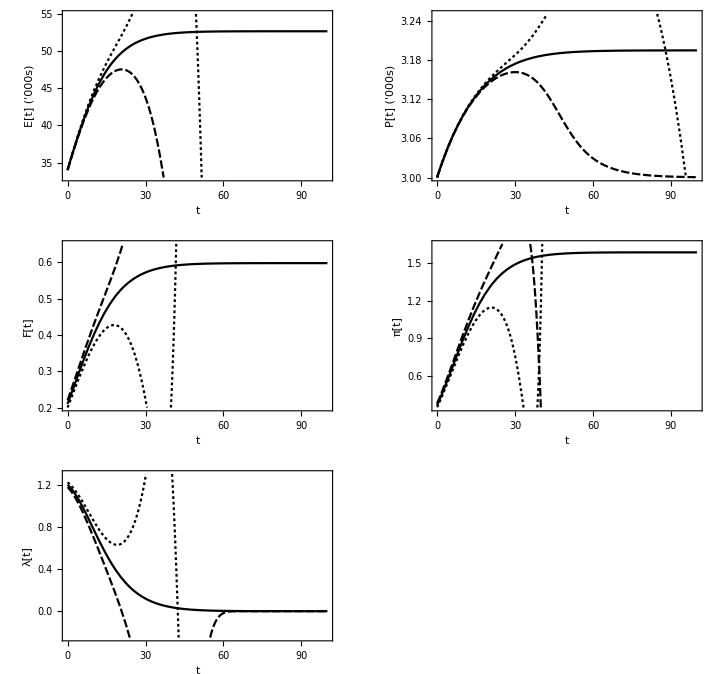

{3.19435}

{52.6731}

{0.597323}

```mathematica
(*Plotting the dynamic model for optimal path*)

Dynamic$Path1[Growth$Elephants_,Elephants$Max_,Hunting_,Eaten_,Growth$Predators_,Predators$Max_,Eating_,Hunting$Efficiency_,Price$Ivory_,c1_,Interest$Rate_,Elasticity1_,Elephants0_, Predators0_,Effort0_]:=NDSolve[
{
(*1*)
(c1 Elasticity1 Elephants$Max Hunting$Efficiency Effort[t]^(2+Elasticity1) Elephants[t]-Hunting$Efficiency Price$Ivory Effort[t]^2 Elephants[t]^2 (2 Growth$Elephants Elephants[t]+Elephants$Max (-Growth$Elephants+Interest$Rate+Eaten Predators[t]))-c1 (-1+Elasticity1) Elasticity1 Elephants$Max Effort[t]^Elasticity1 Elephants[t] Effort'[t]+c1 Elasticity1 Effort[t]^(1+Elasticity1) (2 Growth$Elephants Elephants[t]^2+Elephants$Max Elephants[t] (-Growth$Elephants+Interest$Rate+Eaten Predators[t])+Elephants$Max Elephants'[t]))/(Elephants$Max Hunting$Efficiency Effort[t] Elephants[t])==0,

(*From FOC3*)
Elephants[t] (Growth$Elephants-Hunting$Efficiency Effort[t]-Eaten Predators[t])==(Growth$Elephants Elephants[t]^2)/Elephants$Max+Elephants'[t],

(*Predator growth*)
Growth$Predators*(1-Predators[t]/Predators$Max)*Predators[t]+Eating*Elephants[t]*Predators[t]==Predators'[t],

(*Profit*)Profit1[t]==-c1 (Effort[t])^Elasticity1+Hunting$Efficiency Price$Ivory Effort[t] Elephants[t],

(*CoState*) CoState[t]==(-c1 Elasticity1 Effort[t]^Elasticity1+Hunting$Efficiency Price$Ivory Effort[t] Elephants[t])/(Hunting$Efficiency Effort[t] Elephants[t]),

(*Initial values*)

Elephants[0]==Elephants0,Predators[0]==Predators0, Effort[0]==Effort0 ,Profit1[0]==0,CoState[0]==0

},{Elephants[t], Effort[t],Predators[t],Profit1[t],CoState[t],Elephants'[t]},{t,0,10000} ]



Dynamic$Path1$Plot[t$Max_]:=GraphicsGrid[{

{Plot[{Elephants[t]/.Dynamic$Solution1,Elephants[t]/.Dynamic$Solution2,Elephants[t]/.Dynamic$Solution3},{t,0,t$Max},PlotRange->{33,55},Frame->True,FrameLabel->{"t","E[t] ('000s)"},PlotTheme->"Monochrome"],
Plot[{Predators[t]/.Dynamic$Solution1,Predators[t]/.Dynamic$Solution2,Predators[t]/.Dynamic$Solution3},{t,0,t$Max},PlotRange->{3,3.25},Frame->True,FrameLabel->{"t","P[t] ('000s)"},PlotTheme->"Monochrome"]},

{Plot[{Effort[t]/.Dynamic$Solution1,Effort[t]/.Dynamic$Solution2,Effort[t]/.Dynamic$Solution3},{t,0,t$Max},PlotRange->{0.2,0.65},Frame->True,FrameLabel->{"t","F[t]"},PlotTheme->"Monochrome"],
Plot[{Profit1[t]/.Dynamic$Solution1,Profit1[t]/.Dynamic$Solution2,Profit1[t]/.Dynamic$Solution3},{t,0,t$Max},PlotRange->{0.35,1.65},Frame->True,FrameLabel->{"t","π[t]"},PlotTheme->"Monochrome"]
},

{Plot[{Elephants'[t]/.Dynamic$Solution1,Elephants'[t]/.Dynamic$Solution2,Elephants'[t]/.Dynamic$Solution3},{t,0,t$Max},PlotRange->{-0.25,1.3},Frame->True,FrameLabel->{"t","λ[t]"},PlotTheme->"Monochrome"]}

},Frame->True]

(*Substituting Special Parameters*)

Dynamic$Solution1=Dynamic$Path1@@({Growth$Elephants,Elephants$Max,Hunting,Eaten,Growth$Predators,Predators$Max,Eating,Hunting$Efficiency,Price$Ivory,c1,Interest$Rate,Elasticity1,Elephants0,Predators0,Effort0}/.{Growth$Elephants->0.09,Elephants$Max->200,Hunting->0,Eaten->0.0086,Growth$Predators->0.1,Predators$Max->3,Eating->0.000123,Hunting$Efficiency->0.065,Price$Ivory->1,c1->1,Interest$Rate->0.035,Elasticity1->1.5,Elephants0->34,Predators0->3,Effort0->0.210114026962});

(*Unstable 1*)
Dynamic$Solution2=Dynamic$Path1@@({Growth$Elephants,Elephants$Max,Hunting,Eaten,Growth$Predators,Predators$Max,Eating,Hunting$Efficiency,Price$Ivory,c1,Interest$Rate,Elasticity1,Elephants0,Predators0,Effort0}/.{Growth$Elephants->0.09,Elephants$Max->200,Hunting->0,Eaten->0.0086,Growth$Predators->0.1,Predators$Max->3,Eating->0.000123,Hunting$Efficiency->0.065,Price$Ivory->1,c1->1,Interest$Rate->0.035,Elasticity1->1.5,Elephants0->34,Predators0->3,Effort0->0.22});

(*Unstable 2*)
Dynamic$Solution3=Dynamic$Path1@@({Growth$Elephants,Elephants$Max,Hunting,Eaten,Growth$Predators,Predators$Max,Eating,Hunting$Efficiency,Price$Ivory,c1,Interest$Rate,Elasticity1,Elephants0,Predators0,Effort0}/.{Growth$Elephants->0.09,Elephants$Max->200,Hunting->0,Eaten->0.0086,Growth$Predators->0.1,Predators$Max->3,Eating->0.000123,Hunting$Efficiency->0.065,Price$Ivory->1,c1->1,Interest$Rate->0.035,Elasticity1->1.5,Elephants0->34,Predators0->3,Effort0->0.2});

Dynamic$Path1$Plot[100]

(*Equilibrium Values*)
Predators[t]/.Dynamic$Solution1/.t->100
Elephants[t]/.Dynamic$Solution1/.t->100
Effort[t]/.Dynamic$Solution1/.t->100

Clear[Dynamic$Solution1,Dynamic$Solution2,Dynamic$Solution3]
```

### Increasing cost from 1 to 1.5 in Figure 2.2.2 (Solid line is baseline plot)

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

NDSolve::mconly: For the method NDSolve`IDA, only machine real code is available. Unable to continue with complex values or beyond floating-point exceptions.

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

NDSolve::mconly: For the method NDSolve`IDA, only machine real code is available. Unable to continue with complex values or beyond floating-point exceptions.

ReplaceAll::reps: {Dynamic$Solution3} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

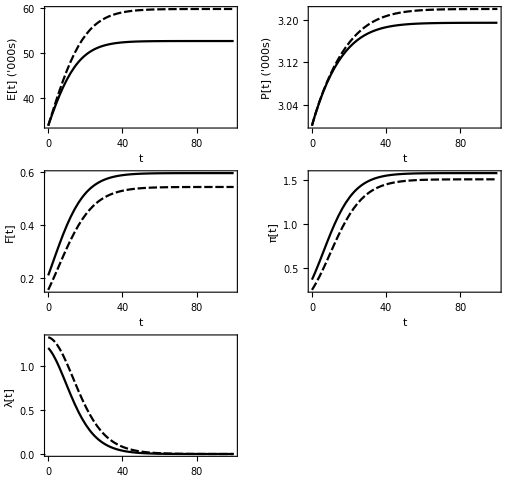

```mathematica
Dynamic$Path1$Plot[t$Max_]:=GraphicsGrid[{

{Plot[{Elephants[t]/.Dynamic$Solution1,Elephants[t]/.Dynamic$Solution2,Elephants[t]/.Dynamic$Solution3},{t,0,t$Max},PlotRange->Full,Frame->True,FrameLabel->{"t","E[t] ('000s)"},PlotTheme->"Monochrome"],
Plot[{Predators[t]/.Dynamic$Solution1,Predators[t]/.Dynamic$Solution2,Predators[t]/.Dynamic$Solution3},{t,0,t$Max},PlotRange->Full,Frame->True,FrameLabel->{"t","P[t] ('000s)"},PlotTheme->"Monochrome"]},

{Plot[{Effort[t]/.Dynamic$Solution1,Effort[t]/.Dynamic$Solution2,Effort[t]/.Dynamic$Solution3},{t,0,t$Max},PlotRange->Full,Frame->True,FrameLabel->{"t","F[t]"},PlotTheme->"Monochrome"],
Plot[{Profit1[t]/.Dynamic$Solution1,Profit1[t]/.Dynamic$Solution2,Profit1[t]/.Dynamic$Solution3},{t,0,t$Max},PlotRange->Full,Frame->True,FrameLabel->{"t","π[t]"},PlotTheme->"Monochrome"]
},

{Plot[{Elephants'[t]/.Dynamic$Solution1,Elephants'[t]/.Dynamic$Solution2,Elephants'[t]/.Dynamic$Solution3},{t,0,t$Max},PlotRange->Full,Frame->True,FrameLabel->{"t","λ[t]"},PlotTheme->"Monochrome"]}

},Frame->True]

Dynamic$Solution1=Dynamic$Path1@@({Growth$Elephants,Elephants$Max,Hunting,Eaten,Growth$Predators,Predators$Max,Eating,Hunting$Efficiency,Price$Ivory,c1,Interest$Rate,Elasticity1,Elephants0,Predators0,Effort0}/.{Growth$Elephants->0.09,Elephants$Max->200,Hunting->0,Eaten->0.0086,Growth$Predators->0.1,Predators$Max->3,Eating->0.000123,Hunting$Efficiency->0.065,Price$Ivory->1,c1->1,Interest$Rate->0.035,Elasticity1->1.5,Elephants0->34,Predators0->3,Effort0->0.210114026962});

Dynamic$Solution2=Dynamic$Path1@@({Growth$Elephants,Elephants$Max,Hunting,Eaten,Growth$Predators,Predators$Max,Eating,Hunting$Efficiency,Price$Ivory,c1,Interest$Rate,Elasticity1,Elephants0,Predators0,Effort0}/.{Growth$Elephants->0.09,Elephants$Max->200,Hunting->0,Eaten->0.0086,Growth$Predators->0.1,Predators$Max->3,Eating->0.000123,Hunting$Efficiency->0.065,Price$Ivory->1,c1->1.5,Interest$Rate->0.035,Elasticity1->1.5,Elephants0->34,Predators0->3,Effort0->0.155384578});

Dynamic$Path1$Plot[100]


Clear[Dynamic$Solution1,Dynamic$Solution2,Dynamic$Solution3]
```

### Increasing ivory price from 1 to 10 in Figure 2.2.2 (Solid line is baseline plot)

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

NDSolve::mconly: For the method NDSolve`IDA, only machine real code is available. Unable to continue with complex values or beyond floating-point exceptions.

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

NDSolve::mconly: For the method NDSolve`IDA, only machine real code is available. Unable to continue with complex values or beyond floating-point exceptions.

ReplaceAll::reps: {Dynamic$Solution3} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

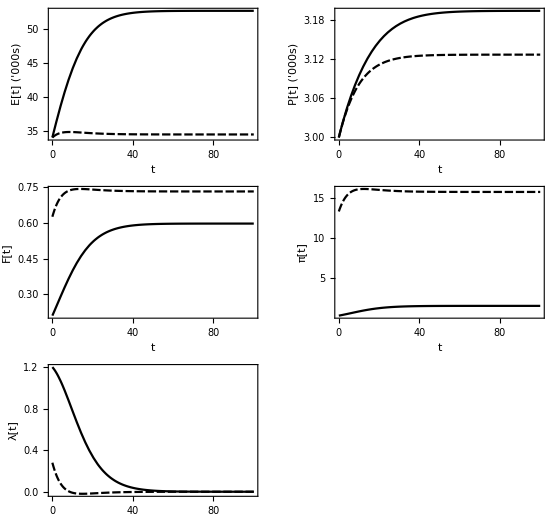

```mathematica
Dynamic$Path1$Plot[t$Max_]:=GraphicsGrid[{

{Plot[{Elephants[t]/.Dynamic$Solution1,Elephants[t]/.Dynamic$Solution2,Elephants[t]/.Dynamic$Solution3},{t,0,t$Max},PlotRange->Full,Frame->True,FrameLabel->{"t","E[t] ('000s)"},PlotTheme->"Monochrome"],
Plot[{Predators[t]/.Dynamic$Solution1,Predators[t]/.Dynamic$Solution2,Predators[t]/.Dynamic$Solution3},{t,0,t$Max},PlotRange->Full,Frame->True,FrameLabel->{"t","P[t] ('000s)"},PlotTheme->"Monochrome"]},

{Plot[{Effort[t]/.Dynamic$Solution1,Effort[t]/.Dynamic$Solution2,Effort[t]/.Dynamic$Solution3},{t,0,t$Max},PlotRange->Full,Frame->True,FrameLabel->{"t","F[t]"},PlotTheme->"Monochrome"],
Plot[{Profit1[t]/.Dynamic$Solution1,Profit1[t]/.Dynamic$Solution2,Profit1[t]/.Dynamic$Solution3},{t,0,t$Max},PlotRange->Full,Frame->True,FrameLabel->{"t","π[t]"},PlotTheme->"Monochrome"]
},

{Plot[{Elephants'[t]/.Dynamic$Solution1,Elephants'[t]/.Dynamic$Solution2,Elephants'[t]/.Dynamic$Solution3},{t,0,t$Max},PlotRange->Full,Frame->True,FrameLabel->{"t","λ[t]"},PlotTheme->"Monochrome"]}

},Frame->True]

Dynamic$Solution1=Dynamic$Path1@@({Growth$Elephants,Elephants$Max,Hunting,Eaten,Growth$Predators,Predators$Max,Eating,Hunting$Efficiency,Price$Ivory,c1,Interest$Rate,Elasticity1,Elephants0,Predators0,Effort0}/.{Growth$Elephants->0.09,Elephants$Max->200,Hunting->0,Eaten->0.0086,Growth$Predators->0.1,Predators$Max->3,Eating->0.000123,Hunting$Efficiency->0.065,Price$Ivory->1,c1->1,Interest$Rate->0.035,Elasticity1->1.5,Elephants0->34,Predators0->3,Effort0->0.210114026962});

Dynamic$Solution2=Dynamic$Path1@@({Growth$Elephants,Elephants$Max,Hunting,Eaten,Growth$Predators,Predators$Max,Eating,Hunting$Efficiency,Price$Ivory,c1,Interest$Rate,Elasticity1,Elephants0,Predators0,Effort0}/.{Growth$Elephants->0.09,Elephants$Max->200,Hunting->0,Eaten->0.0086,Growth$Predators->0.1,Predators$Max->3,Eating->0.000123,Hunting$Efficiency->0.065,Price$Ivory->10,c1->1,Interest$Rate->0.035,Elasticity1->1.5,Elephants0->34,Predators0->3,Effort0->0.626032735624669711693715});

Dynamic$Path1$Plot[100]


Clear[Dynamic$Solution1,Dynamic$Solution2,Dynamic$Solution3]
```

### Figure 2.2.3

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

NDSolve::mconly: For the method NDSolve`IDA, only machine real code is available. Unable to continue with complex values or beyond floating-point exceptions.

ReplaceAll::reps: {Dynamic$Solution2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

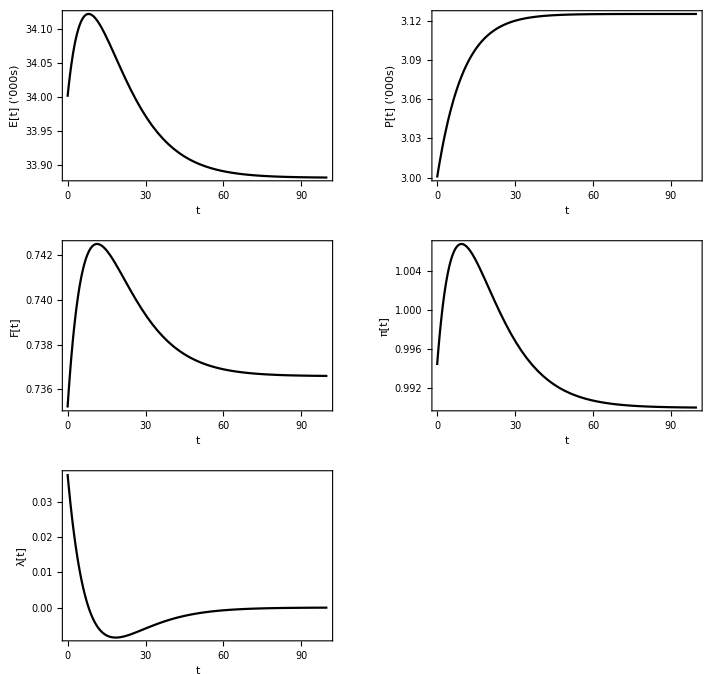

{3.12502}

{33.8817}

{0.736597}

```mathematica
Dynamic$Path1$Plot[t$Max_]:=GraphicsGrid[{

{Plot[{Elephants[t]/.Dynamic$Solution1,Elephants[t]/.Dynamic$Solution2,Elephants[t]/.Dynamic$Solution3},{t,0,t$Max},PlotRange->Full,Frame->True,FrameLabel->{"t","E[t] ('000s)"},PlotTheme->"Monochrome"],
Plot[{Predators[t]/.Dynamic$Solution1,Predators[t]/.Dynamic$Solution2,Predators[t]/.Dynamic$Solution3},{t,0,t$Max},PlotRange->Full,Frame->True,FrameLabel->{"t","P[t] ('000s)"},PlotTheme->"Monochrome"]},

{Plot[{Effort[t]/.Dynamic$Solution1,Effort[t]/.Dynamic$Solution2,Effort[t]/.Dynamic$Solution3},{t,0,t$Max},PlotRange->Full,Frame->True,FrameLabel->{"t","F[t]"},PlotTheme->"Monochrome"],
Plot[{Profit1[t]/.Dynamic$Solution1,Profit1[t]/.Dynamic$Solution2,Profit1[t]/.Dynamic$Solution3},{t,0,t$Max},PlotRange->Full,Frame->True,FrameLabel->{"t","π[t]"},PlotTheme->"Monochrome"]
},

{Plot[{Elephants'[t]/.Dynamic$Solution1,Elephants'[t]/.Dynamic$Solution2,Elephants'[t]/.Dynamic$Solution3},{t,0,t$Max},PlotRange->Full,Frame->True,FrameLabel->{"t","λ[t]"},PlotTheme->"Monochrome"]}

},Frame->True]

(*Substituting Special Parameters*)

Dynamic$Solution1=Dynamic$Path1@@({Growth$Elephants,Elephants$Max,Hunting,Eaten,Growth$Predators,Predators$Max,Eating,Hunting$Efficiency,Price$Ivory,c1,Interest$Rate,Elasticity1,Elephants0,Predators0,Effort0}/.{Growth$Elephants->0.09,Elephants$Max->200,Hunting->0,Eaten->0.0086,Growth$Predators->0.1,Predators$Max->3,Eating->0.000123,Hunting$Efficiency->0.065,Price$Ivory->1,c1->1,Interest$Rate->0.1,Elasticity1->1.5,Elephants0->34,Predators0->3,Effort0->0.73518122496957877265444381009729113429785});

Dynamic$Path1$Plot[100]

(*Equilibrium Values*)
Predators[t]/.Dynamic$Solution1/.t->100
Elephants[t]/.Dynamic$Solution1/.t->100
Effort[t]/.Dynamic$Solution1/.t->100

Clear[Dynamic$Solution1,Dynamic$Solution2,Dynamic$Solution3]
```

Figure 2.2.3

```mathematica
(*Social planner's utility function*)
u[k1_,k2_]:=Log[a1]+α1×Log[k1[t]]+α2×Log[k2[t]]

(*Special Parameters*)
a1=1;
α1=1;
α2=1;

(*Current-Value Hamiltonian*)
H[k1_,k2_,θn_,λ1_,λ2_]:=u[k1,k2]+λ1[t](s (1-θn[t])(k1[t])^a(A×L)^(1-a)-γ×k1[t])+λ2[t](k2[t]×φ(θn[t]^2-θ1))

(*FOC*)
D[H[k1,k2,θn,λ1,λ2],θn[t]]==0//FullSimplify
D[H[k1,k2,θn,λ1,λ2],λ1[t]]==D[k1[t],t]//FullSimplify
D[H[k1,k2,θn,λ1,λ2],λ2[t]]==D[k2[t],t]//FullSimplify
D[H[k1,k2,θn,λ1,λ2],k1[t]]== r×λ1[t]-D[λ1[t],t]//FullSimplify
D[H[k1,k2,θn,λ1,λ2],k2[t]]==r×λ2[t]-D[λ2[t],t]//FullSimplify

(*Solving first FOC*)
Solve[2 φ k2[t] θn[t] λ2[t]==A L (A L)^-a s k1[t]^a λ1[t],λ2[t]]

(*Solving Dynamic equation with the assumption that θn[0]=0.5 *)
SolowSol[s_,A_,a_,L_,γ_,φ_,r_,k10_,k20_,θ1_]:=NDSolve[{γ k1[t]+A L (A L)^-a s k1[t]^a (-1+θn[t])+k1'[t]==0,φ k2[t] (-θ1+θn[t]^2)==k2'[t],1/k1[t]+λ1'[t]==(r+γ+a A L (A L)^-a s k1[t]^(-1+a) (-1+θn[t])) λ1[t],(r+θ1 φ-φ θn[t]^2) λ2[t]==1/k2[t]+λ2'[t],2 φ k2[t] θn[t] λ2[t]==A L (A L)^-a s k1[t]^a λ1[t],k1[0]==k10,k2[0]==k20,λ2[0]==(A L (A L)^-a s k1[0]^a λ1[0])/(φ k2[0]),λ1[0]==10},{k1[t],k2[t],λ1[t],λ2[t],θn[t]},{t,0,50}]

(*Special Parameters with low and high optimal level of conservation*)
Sol1RenRes=SolowSol[0.5,10,0.3,1.1,0.02,0.05,0.5,35,37,0.1];
Sol2RenRes=SolowSol[0.4,10,0.3,1.1,0.02,0.05,0.5,3,35,0.7];
```

2 φ k2[t] θn[t] λ2[t]==A L (A L)^-a s k1[t]^a λ1[t]

γ k1[t]+A L (A L)^-a s k1[t]^a (-1+θn[t])+k1'[t]==0

φ k2[t] (-θ1+θn[t]^2)==k2'[t]

1/k1[t]+λ1'[t]==(r+γ+a A L (A L)^-a s k1[t]^(-1+a) (-1+θn[t])) λ1[t]

(r+θ1 φ-φ θn[t]^2) λ2[t]==1/k2[t]+λ2'[t]

{{λ2[t]→(A L (A L)^-a s k1[t]^a λ1[t])/(2 φ k2[t] θn[t])}}

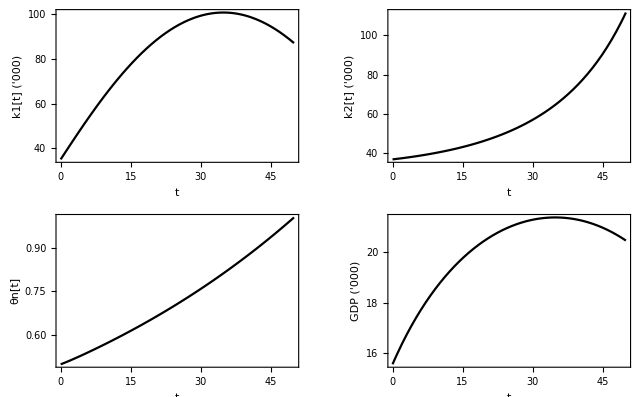

```mathematica
(*Defining GDP of the Economy*)
GDP[k1]:=k1[t]^a×(A L)^(1-a)

(*Plotting the dynamic solutions*)
Dynamic$Path1$Plot:=GraphicsGrid[{
{Plot[k1[t]/.Sol1RenRes ,{t,0,50},PlotRange->Full,Frame->True,FrameLabel->{"t","k1[t] ('000)"}],Plot[k2[t]/.Sol1RenRes,{t,0,50},PlotRange->Full,Frame->True,FrameLabel->{"t","k2[t] ('000)"}]},
{Plot[θn[t]/.Sol1RenRes,{t,0,50},Frame->True,FrameLabel->{"t","θn[t]"}],
Plot[GDP[k1]/.Sol1RenRes/.a->0.3/.A->10/.L->1.1,{t,0,50},Frame->True,FrameLabel->{"t","GDP ('000)"}]}
},Frame->True]
Dynamic$Path1$Plot
```

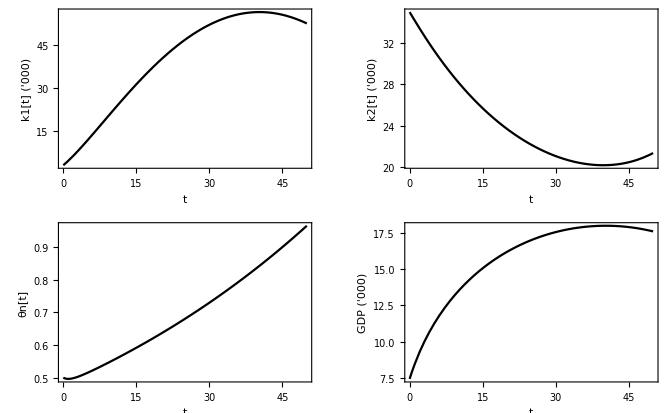

```mathematica
Dynamic$Path2$Plot:=GraphicsGrid[{
{Plot[k1[t]/.Sol2RenRes ,{t,0,50},PlotRange->Full,Frame->True,FrameLabel->{"t","k1[t] ('000)"}],Plot[k2[t]/.Sol2RenRes,{t,0,50},PlotRange->Full,Frame->True,FrameLabel->{"t","k2[t] ('000)"}]},
{Plot[θn[t]/.Sol2RenRes,{t,0,50},Frame->True,FrameLabel->{"t","θn[t]"}],
Plot[GDP[k1]/.Sol2RenRes/.a->0.3/.A->10/.L->1.1,{t,0,50},Frame->True,FrameLabel->{"t","GDP ('000)"}]}
},Frame->True]
Dynamic$Path2$Plot
```